```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
new=RGBColor["#7f0033"];
```

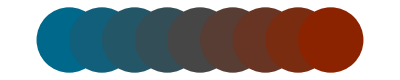

```mathematica
Graphics[Table[{Blend[{BostonBlue,comp},x],Disk[{8x,0}]},{x,0,1,1/8}]]
```

```mathematica
BostonBlue
```

RGBColor[0., 0.40784313725490196, 0.5450980392156862]

```mathematica
(* generate Fibonacci sequence *)
Nest[StringReplace[#,{"A"->"AB","B"->"A"}]&,"A",5]
```

ABAABABAABAAB

```mathematica
(* position along Fibonacci chain *)
τ=N[GoldenRatio];
n[i_]:=Floor[τ^-1 i];
p[i_]:=n[i]Cos[ArcTan[τ^-1]] + (i-n[i])Sin[ArcTan[τ^-1]] ;
```

```mathematica
rect[i_]:=Flatten[{If[n[i+1]-n[i]≥ 1,BostonBlue,{BostonBlue,Opacity[0.5]}],Rectangle[{p[i],0},{p[i+1],1},RoundingRadius->0.2]}]
```

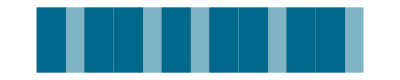

```mathematica
ef=EdgeForm[{new,Thickness[0.01]}];
(*ef=EdgeForm[{Gray,Thickness[0.01]}];*)
ef={};
Graphics[{ef,rect/@Range[1,13]}]
```

```mathematica
Export[NotebookDirectory[]<>"fibo_13.pdf",%]
```

/home/nicolas/git/talks/Phd Day LPS june 2015/fibo_13.pdf